#### Draw mesh

```mathematica
SetDirectory[NotebookDirectory[]]
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Debug"}]]*)
(*SetDirectory["build-converterUNV-Desktop-u041eu0442u043bu0430u0434u043au0430"]*)
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop_Qt_5_10_1_MinGW_32bit-Debug"}]]*)
```

/home/v.korchagova/Документы/BMSTU/RKDG2D

```mathematica
mesh=Import["mesh2D","Table"];
```

```mathematica
(*nodes*)
offset=2;
nNodes=mesh[[offset,1]]
nodes=Table[mesh[[i]],{i,offset+1,nNodes+offset}];
(*edges*)
offset=3+nNodes+1+1;
nEdgesBoundary=mesh[[offset,1]]
nEdges=mesh[[offset+1,1]]
edges=Table[mesh[[i]],{i,offset+2,nEdges+offset+1}];
(*cells*)
offset = offset +nEdges+4;
nCells=mesh[[offset]][[1]]
cells=Table[mesh[[i]],{i,offset+1,nCells+offset}];
(*cell centers*)
offset = offset +nCells+4;
cellCenters=Table[mesh[[i]],{i,offset,nCells+offset-1}];
(*adjoint cells for edges*)
offset = nCells+offset+5;
edgeAdj=Table[mesh[[i]],{i,offset,nEdges+offset-3}];

(*edge normals*)
offset = nEdges+offset+1;
edgeNormals=Table[mesh[[i]],{i,offset,nEdges+offset-1}];
```

1733

126

3447

1715

```mathematica
(*patches*)
offset=offset+nEdges+2;
nPatches=mesh[[offset]][[1]]
offset = offset+1;
patchNames={};
patchEdgeGroups={};
For[i=1,i≤nPatches, ++i,
{
patchNames=Append[patchNames,mesh[[offset,1]]];
(*Print[patchNames];*)
nEdgesInPatch=mesh[[offset+1,1]];
(*Print[nEdgesInPatch];*)
patchEdgeGroups = Append[patchEdgeGroups,Table[mesh[[i,1]],{i,offset+2,offset+1+nEdgesInPatch}]];
offset=offset+2+nEdgesInPatch;
(*Print[offset];*)
}];
patchNames
```

1

{Group_3}

```mathematica
(*drawing functions*)
```

```mathematica
drawNode[iNode_]:=Point[nodes[[iNode]]];
drawEdgeArrow[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeLine[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeNormal[iEdge_]:=Arrow[{(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2,(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2+edgeNormals[[i]]*0.25*Norm[{nodes[[edges[[iEdge,2]]]]-nodes[[edges[[iEdge,1]]]]},2]}];
drawCell[iCell_]:=Polygon[Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[iCell,1]]+1}]];
drawPatch[color_,iPatch_]:={color,Table[drawEdgeLine[patchEdgeGroups[[i,j]]],{j,1,Length[patchEdgeGroups[[i]]]}]};
getCellNodes[iCell_]:=Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[iCell,1]]+1}];
(*areas*)
areas=Table[Area@drawCell[iCell],{iCell,nCells}];
```

```mathematica
(*pictures*)
```

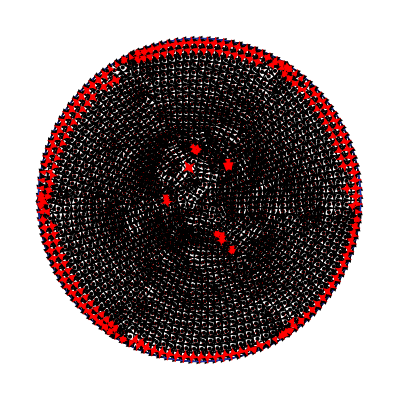

```mathematica
Graphics[{Black,
Table[Point[{cellCenters[[i]]}],{i,1,nCells}],
Table[drawEdgeArrow[i],{i,1,nEdges}],
Red,Arrowheads[0.02],
Table[drawEdgeNormal[i],{i,1,nEdges}],Thick,
Table[drawPatch[RGBColor[i*0.1,i*0.2,i*0.7],i],{i,1,nPatches}]}]
```

```mathematica
Manipulate[Graphics[{Black,Arrowheads[0.02],
Table[drawEdgeArrow[i],{i,1,p}]},PlotRange->All],{p,1,120,1}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[Black],Cyan,
Table[drawCell[i],{i,1,p}],Black,
Table[Point[{cellCenters[[i]]}],{i,1,p}]
},PlotRange->All],{p,1,nCells,1}]
```

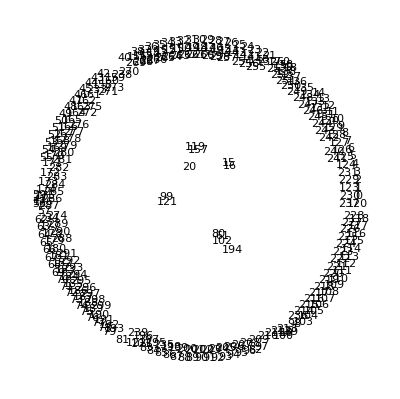

```mathematica
numbers=Graphics[{EdgeForm[Black],Cyan,Opacity[0],
Table[drawCell[i],{i,1,nCells}],Black,Opacity[1],
Table[Text[i-1,cellCenters[[i]]],{i,1,nCells}]
},PlotRange->All]
```

```mathematica
Manipulate[Graphics[{Black,
Table[drawNode[i],{i,{cells[[iCell,2;;2+p]]}}]},PlotRange->Full],{p,0,cells[[iCell,1]]-1,1},{iCell,1,nCells}]
```

#### Basis functions

```mathematica
phi[r_List,iCell_]:={1.0/(√areas[[iCell]]), (r[[1]]-cellCenters[[iCell,1]])/(areas[[iCell]]/(2 √3)),(r[[2]]-cellCenters[[iCell,2]])/(areas[[iCell]]/(2 √3))};
(*phi[r_List,nCell_]:={1.0, r[[1]]-cellCenters[[nCell,1]],r[[2]]-cellCenters[[nCell,2]]};*)
```

```mathematica
gram=Table[Integrate[phi[{x,y},1][[k]]*phi[{x,y},1][[j]],{x,y}∈Polygon[getCellNodes[1]]],{k,3},{j,3}];
gram//MatrixForm
eig=Eigenvalues[gram]
eig[[1]]/eig[[3]]
Det[gram]
```

(1. | 4.05231×10^-15 | -4.05231×10^-15
4.05231×10^-15 | 1. | -5.17401×10^-13
-4.05231×10^-15 | -5.17401×10^-13 | 1.)

{1.,1.,1.}

1.

1.

```mathematica
GetSol[r_List,nCell_,nSol_]:=Sum[alpha[[nCell,nSol,p]]*phi[r,nCell][[p]],{p,1,numFF}]
```

```mathematica
GetSolGraphics[iCell_,nSol_]:=Module[{cNodes},
(cNodes=Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[i,1]]+1}];
Return[Polygon[Table[{cNodes[[i,1]],cNodes[[i,2]],(GetSol[cNodes[[i]],iCell,nSol]-1)},{i,1,cells[[i,1]]}]]]
)]
GetSolGlobal[iCell_,nSol_]:=Module[{cNodes},
(cNodes=Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[i,1]]+1}];
Return[Table[{cNodes[[i,1]],cNodes[[i,2]],GetSol[cNodes[[i]],iCell,nSol]},{i,1,cells[[i,1]]}]]
)]
```

#### Draw solution

```mathematica
(*SetDirectory[FileNameJoin[{ParentDirectory[],"build-RKDG2D-Desktop-u041eu0442u043bu0430u0434u043au0430"}]]*)
SetDirectory[FileNameJoin[{ParentDirectory[],"build-RKDG2D-Desktop-Debug"}]]
```

/home/v.korchagova/Документы/BMSTU/build-RKDG2D-Desktop-Debug

```mathematica
coeffs=Import["alphaCoeffs/0.245000","Table"];
numFF=3;
alpha=Table[Partition[coeffs[[i]],numFF],{i,1,nCells}];
```

```mathematica
Graphics3D[ParallelTable[GetSolGraphics[i,1],{i,1,nCells}]]
```

-Graphics3D-

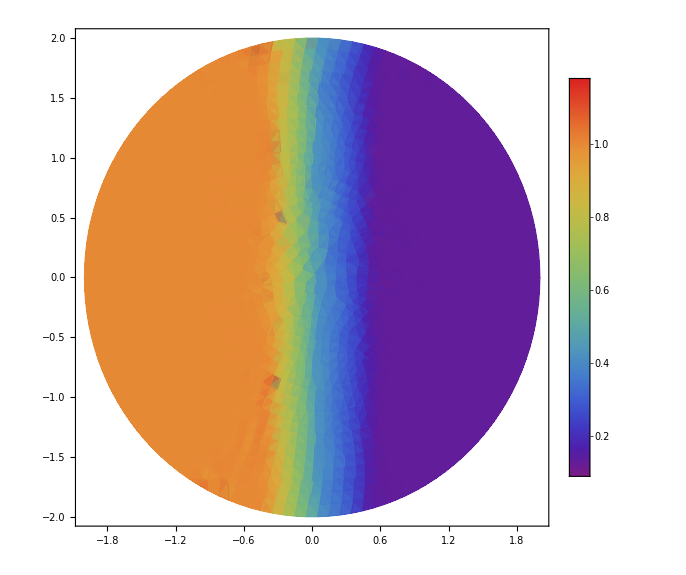

```mathematica
sol=ListDensityPlot[Table[GetSolGlobal[i,1],{i,1,nCells}],PlotRange->Full,ColorFunction->"Rainbow",AspectRatio->Automatic,InterpolationOrder->1,PlotLegends->Automatic,BoundaryStyle->Black,ImageSize->Large]
```

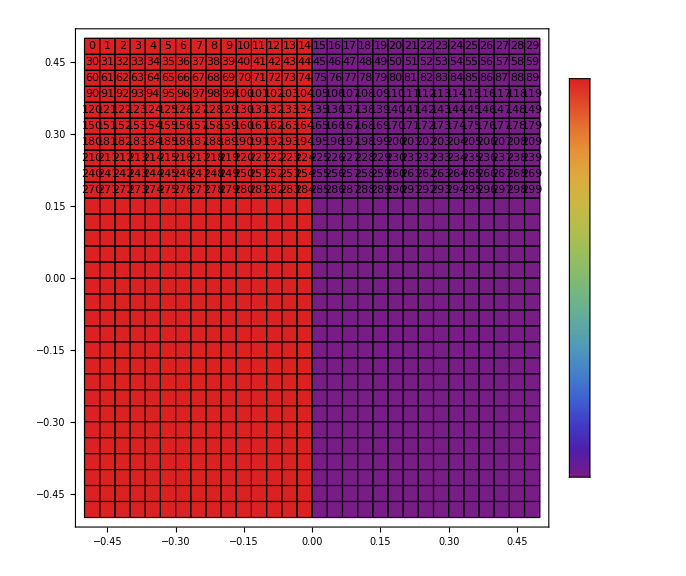

```mathematica
Show[sol,numbers]
```

#### Troubled cells

```mathematica
trCells=Import["troubledCells.txt","Table"]
colors=Table[Cyan,{i,1,nCells}];
colors[[trCells[[1]]+1]]=Red;
```

{{20,25,27,28,29,30,31,32,61,91,92,94,119,143,144,145,146,147,151,194,200,202,203,206,207,258,259,260,310,311,314,316,344,373,374,376,419,420,421,447,453,485,486,490,492,518,531,535,537,540,545,567,569,608,611,628,630,641,644,645,646,703,704,706,708,738,741,744,746,757,762,777,789,794,795,797,803,810,852,855,863,876,883,907,908,913,915,921,922,952,963,967,969,970,974,990,1004,1006,1014,1018,1025,1026,1032,1047,1051,1057,1067,1071,1073,1075,1076,1078,1088,1089,1097,1099,1102,1105,1107,1110,1114,1130,1137,1138,1142,1147,1162,1163,1170,1173,1188,1193,1194,1196,1197,1198,1202,1210,1213,1216,1217,1222,1225,1233,1234,1236,1238,1240,1242,1245,1248,1249,1255,1273,1277,1282,1283,1284,1298,1305,1308,1314,1317,1318,1321,1334,1335,1340,1341,1343,1345,1347,1349,1355,1357,1359,1363,1368,1371,1372,1374,1376,1379,1395,1396,1398,1401,1403,1405,1408,1409,1412,1415,1416,1418,1420,1421,1422,1424,1430,1433,1437,1442,1448,1450,1453,1461,1462,1463,1468,1474,1475,1476,1482,1486,1489,1494,1497,1498,1501,1504,1505,1509,1515,1516,1518,1522,1524,1525,1526,1528,1529,1531,1533,1535,1540,1542,1543,1544,1545,1547,1548,1561,1562,1564,1566,1567,1571,1572,1578,1581,1582,1583,1584,1585,1587,1590,1592,1593,1596,1598,1600,1604,1605,1606,1607,1608,1609,1613,1614,1615,1616,1623,1624,1626,1628,1630,1631,1633,1634,1635,1640,1641,1643,1647,1650,1652,1653,1654,1655,1661,1662,1663,1665,1666,1669,1670,1671,1672,1673,1676,1677,1678,1679,1680,1681,1683,1684,1688,1689,1690,1691,1693,1701,1705,1707,1708,1710,1713,1714}}

Set::partw: Part 908 of … does not exist.

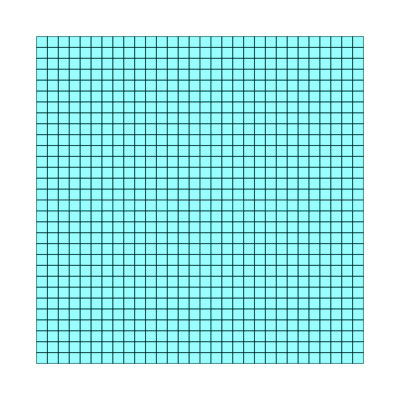

```mathematica
trcells=Graphics[{EdgeForm[Black],Opacity[0.4],
Flatten[Table[{colors[[i]],drawCell[i]},{i,1,nCells}],1]
},PlotRange->All]
```

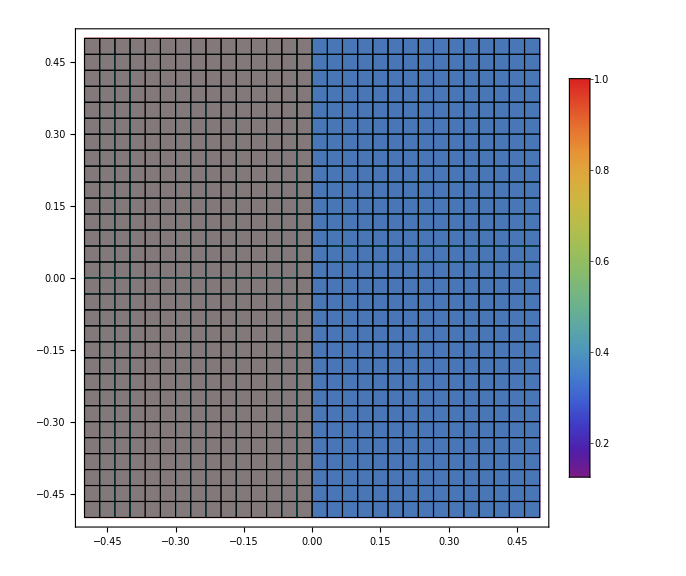

```mathematica
Show[sol,trcells]
```